```mathematica
<<SimpleGroups`
```

Package SimpleGroups (v.0.98β (date:06.05.10)) is loaded

Use SetGroup[] to set the group to work with.

```mathematica
SetGroup[SO[10]]
```

Set group is  D(5)

Rank of the group = 5

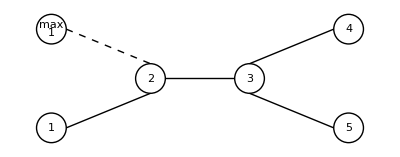

```mathematica
(* We use the SimpleGroups package to realize the Dynkin diagram for SO(10) *)
DynkinDiagram
```

```mathematica
<<GroupMath`
```

paclet:GroupMath/tutorial/GroupMathDoc | XXXXXXXXXXXXXXXXXXXXXXXXXXX GroupMath XXXXXXXXXXXXXXXXXXXXXXXXXXVersion: 1.1.2 (6/May/2020)Author: Renato FonsecaReference: 2011.01764 [hep-th]Website: http://renatofonseca.net/groupmathBuilt-in documentation: paclet:GroupMath/tutorial/GroupMathDocXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX

```mathematica
(* We now employ the GroupMath package to obtain the maximal subalgebras for SO(10) *)
DisplayEmbeddings[MaximalSubgroups[SO10]]
```

{SO8,U1}
(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
2 | 2 | 2 | 1 | 1) | {SU5,U1}
(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
2 | 4 | 6 | 3 | 5) | {SU4,SU2,SU2}
(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
-1 | -2 | -2 | -1 | -1) | {SO5}
(0 | 1 | 3 | 1 | 1
2 | 2 | 0 | 1 | 1) | {SO9}
(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1)
{SO5,SO5}
(1 | 0 | 0 | 0 | 0
0 | 2 | 2 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | -1) | {SO7,SU2}
(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | -1
2 | 2 | 2 | 1 | 1) |  |  |

```mathematica
(* We then use GroupMath to obtain the Cartan matrix for SO(10) *)
SO10//MatrixForm
```

(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | -1
0 | 0 | -1 | 2 | 0
0 | 0 | -1 | 0 | 2)

```mathematica
(* We verify that this inbuilt Cartan matrix is identical to that obtained via SimpleGroups *)
<<SimpleGroupsver098b`
```

Package SimpleGroups (v.0.98β (date:06.05.10)) is loaded

Use SetGroup[] to set the group to work with.

```mathematica
SetGroup[SO[10]]
```

Set group is  D(5)

Rank of the group = 5

```mathematica
CartanMatrix[SimpleRoots]//MatrixForm
```

(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | -1
0 | 0 | -1 | 2 | 0
0 | 0 | -1 | 0 | 2)

```mathematica
SO10 - CartanMatrix[SimpleRoots]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
(* This shows that the Cartan matrices obtained via both packages independently, are indeed identical *)
```

U::shdw: Symbol U appears in multiple contexts {LieART`,Ricci`}; definitions in context LieART` may shadow or be shadowed by other definitions.

A::shdw: Symbol A appears in multiple contexts {LieART`,SimpleGroups`}; definitions in context LieART` may shadow or be shadowed by other definitions.

B::shdw: Symbol B appears in multiple contexts {LieART`,SimpleGroups`}; definitions in context LieART` may shadow or be shadowed by other definitions.

F4::shdw: Symbol F4 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

G2::shdw: Symbol G2 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

E6::shdw: Symbol E6 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

E7::shdw: Symbol E7 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

E8::shdw: Symbol E8 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

CartanMatrix::shdw: Symbol CartanMatrix appears in multiple contexts {LieART`,SimpleGroups`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU::shdw: Symbol SU appears in multiple contexts {LieART`,SimpleGroups`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO::shdw: Symbol SO appears in multiple contexts {LieART`,SimpleGroups`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU2::shdw: Symbol SU2 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU3::shdw: Symbol SU3 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU4::shdw: Symbol SU4 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU5::shdw: Symbol SU5 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU6::shdw: Symbol SU6 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU7::shdw: Symbol SU7 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU8::shdw: Symbol SU8 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU9::shdw: Symbol SU9 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU10::shdw: Symbol SU10 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU11::shdw: Symbol SU11 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU12::shdw: Symbol SU12 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU13::shdw: Symbol SU13 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU14::shdw: Symbol SU14 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU15::shdw: Symbol SU15 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU16::shdw: Symbol SU16 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU17::shdw: Symbol SU17 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU18::shdw: Symbol SU18 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU19::shdw: Symbol SU19 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU20::shdw: Symbol SU20 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU21::shdw: Symbol SU21 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU22::shdw: Symbol SU22 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU23::shdw: Symbol SU23 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU24::shdw: Symbol SU24 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU25::shdw: Symbol SU25 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU26::shdw: Symbol SU26 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU27::shdw: Symbol SU27 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU28::shdw: Symbol SU28 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU29::shdw: Symbol SU29 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU30::shdw: Symbol SU30 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU31::shdw: Symbol SU31 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SU32::shdw: Symbol SU32 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO3::shdw: Symbol SO3 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO5::shdw: Symbol SO5 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO6::shdw: Symbol SO6 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO7::shdw: Symbol SO7 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO8::shdw: Symbol SO8 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO9::shdw: Symbol SO9 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO10::shdw: Symbol SO10 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO11::shdw: Symbol SO11 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO12::shdw: Symbol SO12 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO13::shdw: Symbol SO13 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO14::shdw: Symbol SO14 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO15::shdw: Symbol SO15 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO16::shdw: Symbol SO16 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO17::shdw: Symbol SO17 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO18::shdw: Symbol SO18 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO19::shdw: Symbol SO19 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO20::shdw: Symbol SO20 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO21::shdw: Symbol SO21 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO22::shdw: Symbol SO22 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO23::shdw: Symbol SO23 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO24::shdw: Symbol SO24 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO25::shdw: Symbol SO25 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO26::shdw: Symbol SO26 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO27::shdw: Symbol SO27 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO28::shdw: Symbol SO28 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO29::shdw: Symbol SO29 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO30::shdw: Symbol SO30 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO31::shdw: Symbol SO31 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

SO32::shdw: Symbol SO32 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp2::shdw: Symbol Sp2 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp4::shdw: Symbol Sp4 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp6::shdw: Symbol Sp6 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp8::shdw: Symbol Sp8 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp10::shdw: Symbol Sp10 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp12::shdw: Symbol Sp12 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp14::shdw: Symbol Sp14 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp16::shdw: Symbol Sp16 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp18::shdw: Symbol Sp18 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp20::shdw: Symbol Sp20 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp22::shdw: Symbol Sp22 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp24::shdw: Symbol Sp24 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp26::shdw: Symbol Sp26 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp28::shdw: Symbol Sp28 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp30::shdw: Symbol Sp30 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Sp32::shdw: Symbol Sp32 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

U1::shdw: Symbol U1 appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Weight::shdw: Symbol Weight appears in multiple contexts {LieART`,SimpleGroups`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Rank::shdw: Symbol Rank appears in multiple contexts {LieART`,SimpleGroups`,Ricci`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Bar::shdw: Symbol Bar appears in multiple contexts {LieART`,Ricci`}; definitions in context LieART` may shadow or be shadowed by other definitions.

RootSystem::shdw: Symbol RootSystem appears in multiple contexts {LieART`,SimpleGroups`}; definitions in context LieART` may shadow or be shadowed by other definitions.

PositiveRoots::shdw: Symbol PositiveRoots appears in multiple contexts {LieART`,SimpleGroups`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Index::shdw: Symbol Index appears in multiple contexts {LieART`,Ricci`}; definitions in context LieART` may shadow or be shadowed by other definitions.

ConjugateIrrep::shdw: Symbol ConjugateIrrep appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

DominantWeights::shdw: Symbol DominantWeights appears in multiple contexts {LieART`,GroupMath`}; definitions in context LieART` may shadow or be shadowed by other definitions.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.